## Analyze Article @ Guokr

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/WhyMathematica/Web/WebExtraction/GuokrArticle

Memory Management

```mathematica
(*
ClearMemory:=Module[{},Unprotect[In,Out];Clear[In,Out];Protect[In,Out];ClearSystemCache[];];
*)
```

### Variables

死理性派：http://www.guokr.com/site/logos/

```mathematica
imgSize=700
```

700

### Get All URLs

```mathematica
pageRawData=Import["http://www.guokr.com/site/logos/?page=100","XMLObject",CharacterEncoding->"UTF-8"];
```

```mathematica
pageT=Cases[pageRawData,XMLElement["li",{},{XMLElement["span",{},{pages_}]}]:>ToExpression[pages],Infinity]//Quiet//Last
```

31

```mathematica
sourceRawList=Table[Import[StringJoin["http://www.guokr.com/site/logos/?page=",ToString[i]],"XMLObject",CharacterEncoding->"UTF-8"],{i,1,pageT}];
```

```mathematica
expSourceRawList=Export["sourceRawList.dat",sourceRawList]
```

sourceRawList.dat

```mathematica
sourceTableRaw=Flatten[Table[Cases[sourceRawList[[i]],XMLElement["a",{"shape"->"rect","href"->link_,"target"->"_blank","title"->title_},{whatever_}]:>{title,link},Infinity],{i,1,pageT}],1];
sourceTable=DeleteDuplicates[sourceTableRaw];
ClearAll[sourceTableRaw,sourceRawList]
```

```mathematica
expSourceTable=Export["sourceTable.dat",sourceTable]
```

sourceTable.dat

```mathematica
len=Length@sourceTable
```

313

#### Module of Character Counting

```mathematica
count[url_]:=Module[{aURL=url},
rawD=Import[aURL,"XMLObject",CharacterEncoding->"UTF8"];
cleanUp=Cases[rawD,XMLElement["div",{"class"->"document"},value_]:>value,Infinity];
cleanUp2=Cases[cleanUp,XMLElement["p",{},value_]:>First[value],Infinity];
fD=Delete[cleanUp2,Position[Table[StringMatchQ[ToString@cleanUp2[[i]],StartOfString~~"XMLElement"~~__],{i,1,Length@cleanUp2}],True]];
{Table[StringLength@fD[[i]],{i,1,Length@fD}],Total@Table[StringLength@fD[[i]],{i,1,Length@fD}]}
];
```

#### Count

```mathematica
countTable=First@Import["countTable.xls"];
```

### Analysis

#### Total Number

```mathematica
artList=Table[{StringTake[sourceTable[[i]][[2]],{30,StringLength@sourceTable[[i]][[2]]-1}]},{i,1,len}];
```

```mathematica
countTableAIDT=Table[Append[artList[[i]],countTable[[i]][[2]]],{i,1,len}];
```

```mathematica
countTableT=Table[countTable[[i]][[2]],{i,1,len}];
```

```mathematica
Manipulate[Histogram[countTableT,{a},Frame->True,ChartStyle->"MintColors",ImageSize->imgSize],{a,10,600}]
```

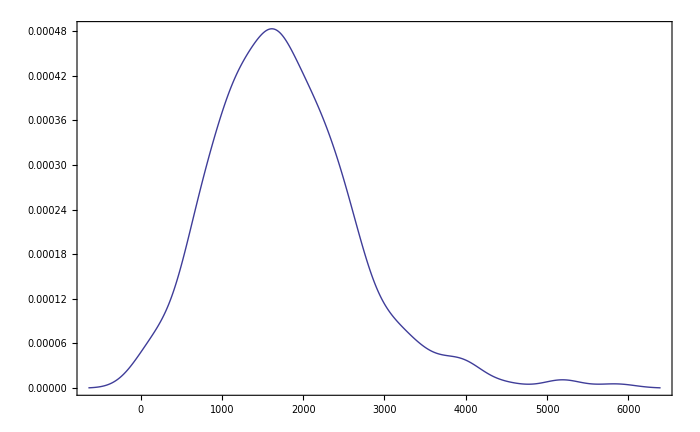

```mathematica
histo=SmoothHistogram[countTableT,Frame->True,ImageSize->imgSize]
```

```mathematica
Manipulate[Plot[100 t^(k/1000) Exp[-t]/((k/1000)!),{k,0,6000},AxesOrigin->{0,0}],{{t,2.6},0.1,5}]
```

```mathematica
Plot[]
```

## Backup

### One Article Test

http : // www.guokr.com/article/437694/

```mathematica
artID="437694";
artURL="http://www.guokr.com/article/"<>ToString[artID]
```

http://www.guokr.com/article/437694

#### Raw Data

```mathematica
rawData=Import[artURL,"XMLObject",CharacterEncoding->"UTF8"];
```

$CharacterEncoding::utf8: The byte sequence {240} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {159} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {152} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding :: utf8 will be suppressed during this calculation.

```mathematica
clean1=Cases[rawData,XMLElement["div",{"class"->"document"},value_]:>value,Infinity];
```

```mathematica
clean2=Cases[clean1,XMLElement["p",{},value_]:>First[value],Infinity];
Length@%
```

47

```mathematica
fdata=Delete[clean2,Position[Table[StringMatchQ[ToString@clean2[[i]],StartOfString~~"XMLElement"~~__],{i,1,Length@clean2}],True]];
```

```mathematica
Table[StringLength@fdata[[i]],{i,1,Length@fdata}]
Total@%
```

{96,23,93,20,151,30,21,61,138,32,81,144,12,114,37,27,48,71,67,62,60,76,17,151,25,17,115,12,12,26,31,11,43,93,196,50,52,11,16,21,70,22,15}

2470

#### Rewrite this into a module

```mathematica
count[url_]:=Module[{aURL=url},
rawD=Import[aURL,"XMLObject",CharacterEncoding->"UTF8"];
cleanUp=Cases[rawD,XMLElement["div",{"class"->"document"},value_]:>value,Infinity];
cleanUp2=Cases[cleanUp,XMLElement["p",{},value_]:>First[value],Infinity];
fD=Delete[cleanUp2,Position[Table[StringMatchQ[ToString@cleanUp2[[i]],StartOfString~~"XMLElement"~~__],{i,1,Length@cleanUp2}],True]];
{Table[StringLength@fD[[i]],{i,1,Length@fD}],Total@Table[StringLength@fD[[i]],{i,1,Length@fD}]}
];
```

```mathematica
count[artURL]
```

$CharacterEncoding::utf8: The byte sequence {240} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {159} could not be interpreted as a character in the UTF-8 character encoding.

$CharacterEncoding::utf8: The byte sequence {152} could not be interpreted as a character in the UTF-8 character encoding.

General::stop: Further output of $CharacterEncoding :: utf8 will be suppressed during this calculation.

{{96,23,93,20,151,30,21,61,138,32,81,144,12,114,37,27,48,71,67,62,60,76,17,151,25,17,115,12,12,26,31,11,43,93,196,50,52,11,16,21,70,22,15},2470}

## Draft

#### Raw Data

```mathematica
rawData=Import[artURL,"XMLObject",CharacterEncoding->"UTF-8"];
```

```mathematica
clean1=Cases[Import[artURL,"XMLObject",CharacterEncoding->"UTF-8"],XMLElement["div",{"class"->"document"},value_]:>value,Infinity];
```

```mathematica
clean2=Cases[Cases[Import[artURL,"XMLObject",CharacterEncoding->"UTF-8"],XMLElement["div",{"class"->"document"},value_]:>value,Infinity],XMLElement["p",{},value_]:>First[value],Infinity];
Length@%
```

47

```mathematica
fdata=Delete[clean2,Position[Table[StringMatchQ[ToString@clean2[[i]],StartOfString~~"XMLElement"~~__],{i,1,Length@clean2}],True]];
```

```mathematica
Table[StringLength@fdata[[i]],{i,1,Length@fdata}]
Total@%
```

{96,23,93,20,151,30,21,61,138,32,81,144,12,114,37,27,48,71,67,62,60,76,17,151,25,17,115,12,12,26,31,11,43,93,196,50,52,11,16,21,70,22,15}

2470